### Categorization

Symbol

BiGridGenerator

BiGridGenerator`

BiGridGenerator/ref/SortPlay

### Keywords

### Syntax Templates

Details

# SortPlay

SortPlay[{List}]
SortPlay[{List}]使用柱状图播放排序过程.
   SortDraw[{List}]
SortDraw[{List}]使用状态矩阵显示排序过程.
   SortPlot[{List}]
SortPlot[{List}]使用对应点状图显示排序过程.
   SortShow[{List}]
SortShow[{List}]使用线路图显示排序过程.
   BeadSortStep[Matrix]
BeadSortStep[Matrix]给出状态矩阵Matrix的珠排的逐步过程.
   BeadPlay[List]
BeadPlay[List]播放List的状态矩阵的排序过程

## Tutorials

## Related Links

## See Also

NLimit ▫ NSeries ▫ D ▫ NResidue

## More About

## Examples | More Examples ⊳

```mathematica
Needs["SortPlay`"]
```

直观的显示在默认物理法则下珠排的过程

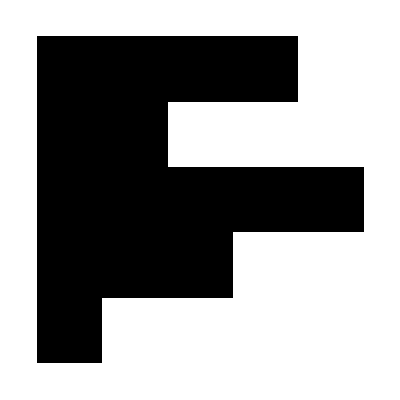

```mathematica
ArrayPlot[step={{1,1,1,1,0},{1,1,0,0,0},{1,1,1,1,1},{1,1,1,0,0},{1,0,0,0,0}}]
```

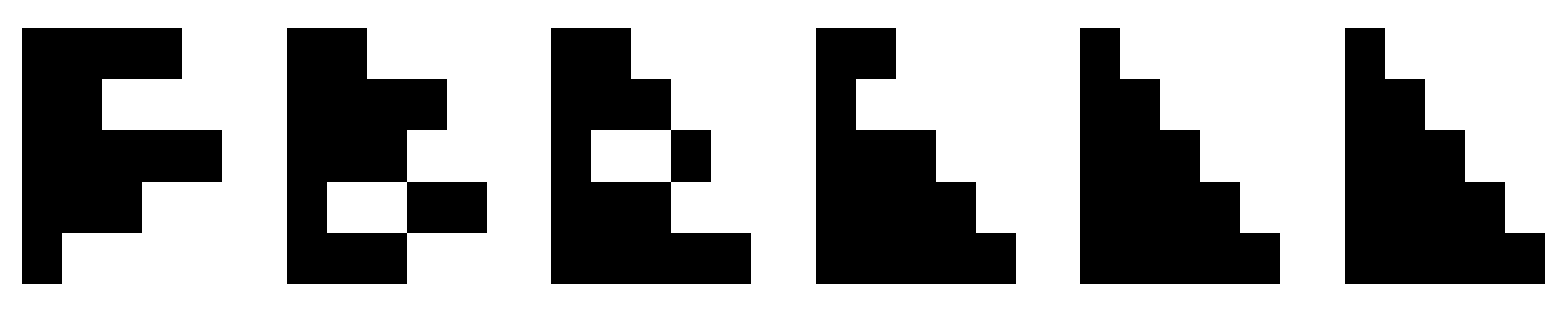

```mathematica
GraphicsRow[ArrayPlot/@FixedPointList[BeadSortStep,step]]
```

将上面的过程制成动画

```mathematica
BeadPlay[{4,2,5,3,1}]
```

$CellContext`i3$$Typeset`show$$Typeset`bookmarkList$$Typeset`bookmarkMode$$Typeset`animator$$Typeset`animvar$$Typeset`name$$Typeset`specs$$Typeset`size$$Typeset`update$$Typeset`initDone$$Typeset`skipInitDone$$$CellContext`i3$4532$$

## More Examples

### 巧妙范例

```mathematica
Needs["SortPlay`"]
```

用不同的方式显示一个排序过程:

```mathematica
start=RandomSample@Range@10
```

{7,4,2,5,9,8,3,1,10,6}

```mathematica
process=QuickSort@start
```

{{7,4,2,5,9,8,3,1,10,6},{4,2,5,3,1,6,7,9,8,10},{2,3,1,4,5,6,7,9,8,10},{1,2,3,4,5,6,7,9,8,10},{1,2,3,4,5,6,7,8,9,10}}

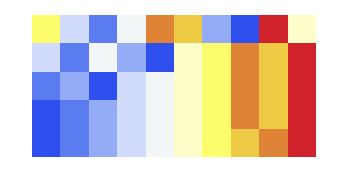
{SortAlgorithm`Private`n$$Typeset`show$$Typeset`bookmarkList$$Typeset`bookmarkMode$$Typeset`animator$$Typeset`animvar$$Typeset`name$$Typeset`specs$$Typeset`size$$Typeset`update$$Typeset`initDone$$Typeset`skipInitDone$$SortAlgorithm`Private`n$6378$$,-Graphics-,SortAlgorithm`Private`n$$Typeset`show$$Typeset`bookmarkList$$Typeset`bookmarkMode$$Typeset`animator$$Typeset`animvar$$Typeset`name$$Typeset`specs$$Typeset`size$$Typeset`update$$Typeset`initDone$$Typeset`skipInitDone$$SortAlgorithm`Private`n$6395$$,-Graphics-}

```mathematica
Through[{SortPlay,SortDraw,SortPlot,SortShow}[process]]
```

比较不同算法下的排序过程:

```mathematica
start=RandomSample@Range@25;
list={BubbleSort,InsertionSort,CocktailSort,ShellSort,QuickSort,BeadSort[#,"延迟匀速"]&,BeadSort[#,"延迟光速"]&,BeadSort[#,"瞬时匀速"]&,BeadSort[#,"瞬时光速"]&};
processes=Through[list[start]];
```

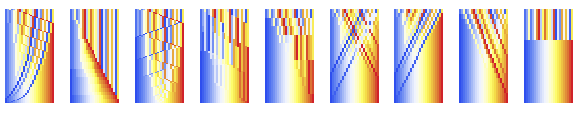

```mathematica
GraphicsRow[SortDraw/@processes]
```

### 算法效率测算

安全性取决于所用的排序算法.